```mathematica
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/Frenkels_classifier_dataSet/pdf_ALL_results/"];
filesTrain={"pdf_OUT_129.4850/pdf.129.4850.300.1_1141.txt","pdf_OUT_142.4850/pdf.142.4850.300.1_891.txt",
"pdf_OUT_70.4850/m.pdf.70.4850.300.1_842.txt","pdf_OUT_174.4850/pdf.174.4850.300.1_851.txt",
"pdf_OUT_1126.4850/pdf.1126.4850.300.1_746.txt","pdf_OUT_perf.4850/m.pdf.PERF.4850.300.1_1071.txt"};


(*files={"pdf.70.4850.1_836.txt","pdf.129.4850.1_1141.txt","pdf.142.4850.1_891.txt","pdf.174.4850.1_851.txt","pdf.1126.4850.1_746.txt","pdf.PERF.4850.1_1071.txt"};*)
pdfData=Table[ReadList[filesTrain[[i]],{Number,Number,Number,Number,Number}],{i,1,6}];

names={"129","142","70","174","1126","PERF"};
temperatures={"300","760","1900","2500","3200","3805"};
fullNames={"Bound-dimer","Bound-trimer","Unbound-dimer","Unbound-trimer","Unbound-tetramer","Perfect"};
header={"Methods","Bound-dimer","Bound-trimer","Unbound-dimer","Unbound-Trimer","Unbound-Tetramer","Perfect"};
(*volumes={"V=V(0.75T_C)","V=V(0.9T_C)"};*)

zrzr=Table[Transpose@{Transpose[pdfData[[i]]][[1]],Transpose[pdfData[[i]]][[2]]},{i,1,6}];
czr=Table[Transpose@{Transpose[pdfData[[i]]][[1]],Transpose[pdfData[[i]]][[3]]},{i,1,6}];
cc=Table[Transpose@{Transpose[pdfData[[i]]][[1]],Transpose[pdfData[[i]]][[4]]},{i,1,6}];
tot=Table[Transpose@{Transpose[pdfData[[i]]][[1]],Transpose[pdfData[[i]]][[5]]},{i,1,6}];
all=Table[Transpose@{Transpose[pdfData[[i]]][[2]],Transpose[pdfData[[i]]][[3]],Transpose[pdfData[[i]]][[4]]},{i,1,6}];
ccczr=Table[Transpose@{Transpose[pdfData[[i]]][[1]],Transpose[pdfData[[i]]][[4]],Transpose[pdfData[[i]]][[3]]},{i,1,6}];
ccczrzrzr=Table[Transpose@{Transpose[pdfData[[i]]][[1]],Transpose[pdfData[[i]]][[4]],Transpose[pdfData[[i]]][[3]],Transpose[pdfData[[i]]][[2]]},{i,1,6}];

methods={"LogisticRegression","Markov","NaiveBayes","NearestNeighbors","RandomForest","SupportVectorMachine"}
methodsProduction={"LogisticRegression","SupportVectorMachine"}

plotStyleA={PlotRange->All,PlotTheme->"Scientific",Frame->True,PlotStyle->Directive[Black,Thickness[0.006]],FrameLabel->{Style["r (Å)",18,Black],Style["ρ(r, t)",18,Black]},FrameStyle->Directive[18,Black,Thickness[0.004]]};


proSum={#[[1]],0.5*(#[[3]]+#[[4]])}&;
proSum2={#[[1]],(#[[4]])}&;
```

{LogisticRegression,Markov,NaiveBayes,NearestNeighbors,RandomForest,SupportVectorMachine}

{LogisticRegression,SupportVectorMachine}

```mathematica
Module[{maxTempsTrain=6,maxTempsTest=6,maxTypes=6},

cSVMlin=With[{method=methodsProduction[[1]]},
(*Define a training set*)
trainingSet=Table[Table[Table[proSum/@Partition[pdfDataProTest[[type]][[temp]],81][[timeStep]]->ToString@fullNames[[type]],{timeStep,1,Length@Partition[pdfDataProTest[[type]][[temp]],81]}],{temp,1,maxTempsTrain}],{type,1,maxTypes}];

(*Collapse the training set dimensions into one big set*)
twoTempsTrainingFlat=Join@@Join@@trainingSet;
(*Run the classifier*)
Classify[twoTempsTrainingFlat,Method->method,PerformanceGoal->"Quality"]
];

(*Model testing*)
With[{method=methodsProduction[[1]]},

(*Define the teseting or validation data set*)
valData=Table[Table[Table[proSum/@Partition[pdfDataProTest[[type]][[temp]],81][[timeStep]],{timeStep,1,Length@Partition[pdfDataProTest[[type]][[temp]],81]}],{temp,1,maxTempsTest}],{type,1,maxTypes}];

(*Apply the model to a test set*)
results=Table[Table[Table[cSVMlin[valData[[type]][[temp]][[timeStep]]],{timeStep,1,Length@valData[[type]][[temp]]}],{temp,1,maxTempsTest}],{type,1,maxTypes}];

(*Results presentation*)
accuracy=Table[Table[Count[results[[type]][[temp]],fullNames[[type]]]/Length[results[[type]][[temp]]]//N,{temp,1,maxTempsTest}],{type,1,maxTypes}];
tList=Table[temperatures[[temp]],{temp,1,maxTempsTest}];
typeList=Table[fullNames[[type]],{type,1,maxTypes}];
typeListTemps=Join@@{{"Temperatures:"},typeList};
message=StringJoin["Model type: ",ToString@method,", with training temperatures (K): ",ToString@tList[[1;;maxTempsTrain]]];
(*{message,Join@@{{typeListTemps},Transpose@Join[{tList},accuracy]}}//TableForm*)
{{message},Transpose[Join@@{{typeListTemps},Transpose@Join[{tList},accuracy]}]//TableForm}//TableForm
]
]
```

Model type: LogisticRegression, with training temperatures (K): {300, 760, 1900, 2500, 3200, 3805}
Temperatures: | 300 | 760 | 1900 | 2500 | 3200 | 3805
Bound-dimer | 1. | 1. | 0.981481 | 0.977778 | 1. | 0.928571
Bound-trimer | 1. | 0.967742 | 0.972973 | 0.807339 | 0.833333 | 0.95
Unbound-dimer | 1. | 1. | 0.994083 | 1. | 1. | 0.975207
Unbound-trimer | 1. | 0.964912 | 0.964467 | 0.933735 | 0.925926 | 0.879747
Unbound-tetramer | 1. | 1. | 0.971014 | 1. | 0.925926 | 1.
Perfect | 1. | 1. | 1. | 1. | 0.96875 | 1.

### Test data

```mathematica
(*Bound*)
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/Frenkels_classifier_dataSet/pdf_ALL_results/pdf_OUT_129.4850/normal/full_version"];
filesTestVal129={"m.pdf.129.4850.760.B2-01_129.B3-130_154.txt","m.pdf.129.4850.1900.B2-01_108.B3-109_179.txt","m.pdf.129.4850.2500.B2-01_45.B3-46-128.txt",
"m.pdf.129.4850.3200.B2-01_30.B3-30-137.txt"};
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/Frenkels_classifier_dataSet/pdf_ALL_results/pdf_OUT_142.4850/normal/full_version"];
filesTestVal142={"m.pdf.142.4850.1900.B3-01_111.B4-112_156.B3-157_199.txt","m.pdf.142.4850.2500.B3-01_109.B4-110_124.B3-125_140.B2-141_142.B3-143_146.B2-147_157.B3-158_176.txt",
"m.pdf.142.4850.3200.B3-01_60.B2-61_64.B3-65_123.B4-124_133.B3-134_183.txt","m.pdf.142.4850.3805.B3-01_20.B2-21_114.B3-115_143.txt"};

(*Unbound*)
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/Frenkels_classifier_dataSet/pdf_ALL_results/pdf_OUT_70.4850/normal/full_version"];
filesTestVal70={"m.pdf.70.4850.3200.U2-01_169.U3-170_185.txt","m.pdf.70.4850.3805.U2-01_121.U3-122_131.U4-132_143.U3-144_172.txt"};

SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/Frenkels_classifier_dataSet/pdf_ALL_results/pdf_OUT_174.4850/normal/full_version"];
filesTestVal174={"m.pdf.174.4850.3200.U3-01_81.U2-82_92.U3-93_166.U2-167_170.U3-171_185.txt","m.pdf.174.4850.3805.U3-01_158.U4-159_181.txt"};

SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/Frenkels_classifier_dataSet/pdf_ALL_results/pdf_OUT_1126.4850/normal/full_version"];
filesTestVal1126={"m.pdf.1126.4850.760.U4-01_176.U3-177-187.txt","m.pdf.1126.4850.1900.U4-01_69.U3-70_164.txt","m.pdf.1126.4850.2500.U4-01_67.U3-68_157.txt","m.pdf.1126.4850.3200.U4-01_54.U3-55_153.txt"};

filesDefectTypesVal={filesTestVal129,filesTestVal142,filesTestVal70,filesTestVal174,filesTestVal1126};
dirList={"/Volumes/MicroSD/2_PostDoc_SD/Frenkels_classifier_dataSet/pdf_ALL_results/pdf_OUT_129.4850/normal/full_version","/Volumes/MicroSD/2_PostDoc_SD/Frenkels_classifier_dataSet/pdf_ALL_results/pdf_OUT_142.4850/normal/full_version","/Volumes/MicroSD/2_PostDoc_SD/Frenkels_classifier_dataSet/pdf_ALL_results/pdf_OUT_70.4850/normal/full_version","/Volumes/MicroSD/2_PostDoc_SD/Frenkels_classifier_dataSet/pdf_ALL_results/pdf_OUT_174.4850/normal/full_version","/Volumes/MicroSD/2_PostDoc_SD/Frenkels_classifier_dataSet/pdf_ALL_results/pdf_OUT_1126.4850/normal/full_version"};
pdfDataProTestVal=Table[Table[SetDirectory[dirList[[type]]];ReadList[filesDefectTypesVal[[type]][[temp]],{Number,Number,Number,Number,Number}],{temp,1,Length@filesDefectTypesVal[[type]]}],{type,1,5}];

CCdataSet=Table[Table[proSum2/@pdfDataProTestVal[[1]][[temp]],{temp,1,Length@filesDefectTypesVal[[type]]}],{type,1,5}];
```

```mathematica
testingValSet=Table[Table[Table[proSum/@Partition[pdfDataProTestVal[[type]][[temp]],81][[timeStep]],{timeStep,1,Length@Partition[pdfDataProTestVal[[type]][[temp]],81]}],{temp,1,filesDefectTypesVal[[type]]//Length}],{type,1,filesDefectTypesVal//Length}];
modelResults=Table[Table[Table[cSVMlin[testingValSet[[type]][[temp]][[timeStep]]],{timeStep,1,Length@testingValSet[[type]][[temp]]}],{temp,1,Length@testingValSet[[type]]}],{type,1,Length@testingValSet}];
```

```mathematica
rule=Table[fullNames[[i]]->i,{i,1,Length@fullNames}]
tickS=Table[{i,Style[fullNames[[i]],18,Black]},{i,1,Length@fullNames}];
```

{Bound-dimer→1,Bound-trimer→2,Unbound-dimer→3,Unbound-trimer→4,Unbound-tetramer→5,Perfect→6}

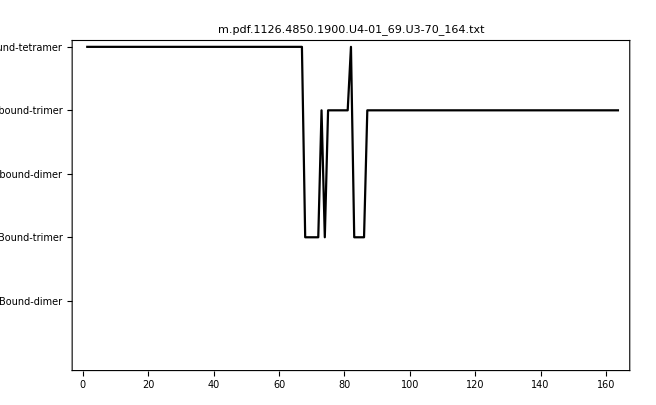

```mathematica
With[{temp=2,type=5},ListLinePlot[modelResults[[type]][[temp]]/.rule,PlotRange->All,PlotLabel->Style[filesDefectTypesVal[[type]][[temp]],12,Black],PlotStyle->Black,FrameStyle->Directive[18,Thickness[0.006],Black],FrameTicks->{{tickS,None},Automatic},PlotRange->{Automatic,{0,6}},Frame->True]]
```

```mathematica
proSumDelta={#[[1]],(#[[4]])/#[[1]]}&;
```

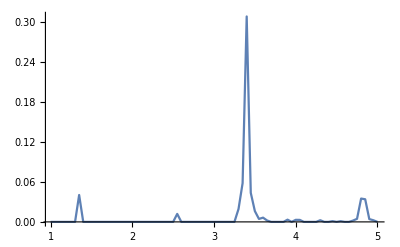

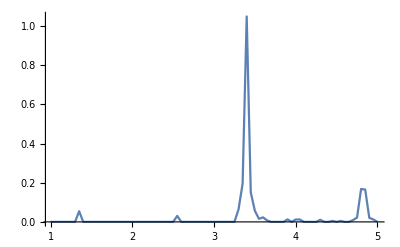

```mathematica
ListLinePlot[proSumDelta/@Partition[pdfDataProTest[[1]][[1]],81][[1]],PlotRange->All]
ListLinePlot[proSum2/@Partition[pdfDataProTest[[1]][[1]],81][[1]],PlotRange->All]
```

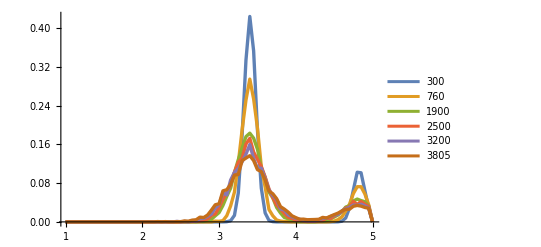

```mathematica
ListLinePlot[Table[Table[Mean@Table[proSum2/@Partition[pdfDataProTest[[type]][[temp]],81][[timeStep]],{timeStep,1,Length@Partition[pdfDataProTest[[type]][[temp]],81]}],{temp,1,6}],{type,6,6}][[1]],PlotRange->All,PlotLegends->temperatures,PlotStyle->Thickness[0.006]]
```

```mathematica
3
```